```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../setup.nb"]
```

```mathematica
abortOnMessageOn[]
```

```mathematica
Get[NotebookDirectory[]<>"../../Data/WT/mesh-data.mx"];
```

## Find cell quartets that undergo T1 transitions

#### Find cell quartets across all frames

Identify cell quartets by finding all 4-cycles in the neighborhood graph of cells. “Align” all the cycles to a canonical ordering such that they can be tracked over time

```mathematica
alignCycle[c_]:=With[{cc=RotateLeft[c,First@FirstPosition[c,Min[c]]-1]},
Prepend[
If[
cc[[2]]<cc[[-1]],
Rest[cc],
Reverse[Rest[cc]]
],
First[cc]
]
]
```

```mathematica
allQuartetsRaw=Monitor[Catenate@Table[
Thread[{t,alignCycle/@VertexList/@FindCycle[makeGraph[bodyCells,cellNeighborsTS[[t]]],{4},All]}],{t,Length[cellNeighborsTS]}
],t];//AbsoluteTiming
```

{645.663,Null}

In some rare cases, small cells are surrounded by a four-cell loop. These instances need to be removed.

```mathematica
checkForSurroundedCell[cells_,t_]:=With[{
neighborhood=getNeighborhood[cells,t,2]
(* We have to go the second order neighborhood because there might be degenerate vertices along the ring of first order neighbors *)
},
Or[
(* Check if one of the cells is surrounded by the rest *)
Or@@Table[Sort[cellNeighborsTS[[t]][cells[[i]]]]==Sort[Delete[cells,i]],{i,Length[cells]}],
(* Check if the cells surround some other cell *)
Length@ConnectedComponents[VertexDelete[makeGraph[neighborhood,cellNeighborsTS[[t]]],cells]]>1
]
]
```

```mathematica
allQuartets=Select[allQuartetsRaw,!checkForSurroundedCell[#[[2]],#[[1]]]&];//AbsoluteTiming
```

{1811.09,Null}

```mathematica
Take[allQuartets,3]
```

{{1,{14564,14610,14702,14642}},{1,{14522,14564,14642,14610}},{1,{14466,14522,14610,14564}}}

```mathematica
quartetExistsTimes=#[[All,1]]&/@GroupBy[allQuartets,Last];
```

```mathematica
quartetExistsIntervals=findContinuousIntervals/@quartetExistsTimes;
```

#### Tracking intercalations

```mathematica
(*sharedVertices[cells_,t_]:=Intersection@@(If[MissingQ[#],Return[{}],#]&@cellVerticesTS[[t]][#]&/@cells)*)
```

Identify the pair of cells in a quartet that are in contact. They form the “inner edge”. By tracking the inner edge in quartet over time, we can identify T1 events

```mathematica
quartetInnerEdge[quartet_:{_Integer..},t_]:=With[{},
If[MemberQ[cellNeighborsTS[[t]][quartet[[1]]],quartet[[3]]],
Return[{quartet[[1]],quartet[[3]]}]
];
If[MemberQ[cellNeighborsTS[[t]][quartet[[2]]],quartet[[4]]],
Return[{quartet[[2]],quartet[[4]]}]
];
{}
]
```

```mathematica
firstT1Intervals=First@Last@Reap[KeyValueMap[Function[{quartet,intervals},
(* Only consider quartets that change topology between the first time and the last time they exist *)
If[quartetInnerEdge[quartet,intervals[[1,1]]]!=quartetInnerEdge[quartet,intervals[[-1,-1]]],
Scan[
If[quartetInnerEdge[quartet,#[[1]]]=!=quartetInnerEdge[quartet,#[[2]]],
Sow[quartet->#];Return[None,Scan]]&,
intervals
]]
],
quartetExistsIntervals
]];//AbsoluteTiming
```

{1.37775,Null}

```mathematica
firstT1Intervals//Length
```

2933

```mathematica
findT1[quartet_,{t0_,t1_}]:=Module[{
initEdge=quartetInnerEdge[quartet,t0],
event=Missing["NoT1",quartet]
},
Do[
If[initEdge=!=quartetInnerEdge[quartet,t],event={t,initEdge,quartetInnerEdge[quartet,t]};Break[]],
{t,t0+1,t1}
];
event
]
```

```mathematica
firstT1Times=Association[KeyValueMap[#1->findT1[##]&,Association@firstT1Intervals]];
```

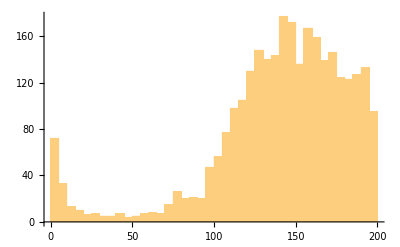

```mathematica
Histogram[firstT1Times[[All,1]],{5}]
```

#### Tracking inner edge length

```mathematica
innerEdgeLength[quartet_,t_]:=If[#=={},0.,sharedEdgeLength[#,t]]&@quartetInnerEdge[quartet,t]
```

Encode neighbor exchange by the sign of the edge length, with negative length indicating that it deviates from the length at the beginning of the consecutive interval. Is is really only sensible for quartets.

Track edge length for a given interval

```mathematica
trackInnerEdgeLength[quartet_,{ts_,te_}]:=With[{
initEdge=Do[(* Look for the first time there is a shared edge *)
If[#=!={},Return[#]]&@quartetInnerEdge[quartet,t],
{t,ts,te}
]
},
Table[
{t,If[#=={},0.,If[#===initEdge,1,-1]sharedEdgeLength[#,t]]&@quartetInnerEdge[quartet,t]},
{t,ts,te}]
]
```

```mathematica
quartetExistsIntervals[{19347,19413,19511,19475}]
```

{{1,1},{3,198}}

```mathematica
Take[quartetExistsIntervals,2]
```

<|{14564,14610,14702,14642}→{{1,21},{23,24},{37,38},{40,83},{86,87},{90,118}},{14522,14564,14642,14610}→{{1,134},{136,136}}|>

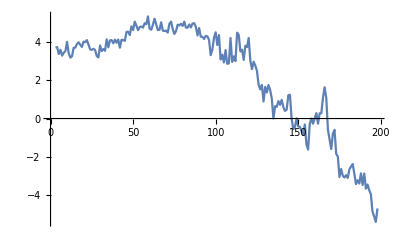

```mathematica
ListLinePlot[trackInnerEdgeLength[{19347,19413,19511,19475},{3,198}]]
```

Track edge length for a all existence intervals of a quartet

```mathematica
trackInnerEdgeLength[quartet_]:=Module[{
intervals=quartetExistsIntervals[quartet],
initEdge
},
initEdge=Do[(* Look for the first time there is a shared edge *)
If[#=!={},Return[#]]&@quartetInnerEdge[quartet,t],
{t,Catenate[Range@@#&/@intervals]}
];
Table[
Table[
{t,If[#=={},0.,If[#===initEdge,1,-1]sharedEdgeLength[#,t]]&@quartetInnerEdge[quartet,t]},
{t,interval[[1]],interval[[2]]}],
{interval,intervals}
]
]
```

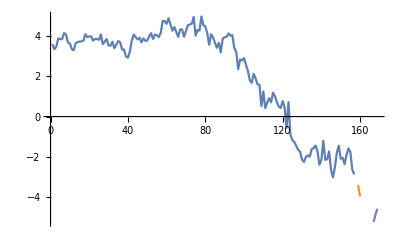

```mathematica
ListLinePlot[trackInnerEdgeLength[Keys[quartetExistsIntervals][[17]]]]
```

Short lived quartets are those than transiently form within rosettes. They are not relevant for the analysis here.

```mathematica
quartetInnerEdgeLength=Association@KeyValueMap[#1->trackInnerEdgeLength[#1]&,Select[
(* Select quartets that exist for more than 20 frames in total *)
quartetExistsIntervals,
Max[(#[[2]]-#[[1]]+1)&/@#]>20&]
];//AbsoluteTiming
```

{21.9592,Null}

```mathematica
signChangePosition[list_]:=First/@Position[Times@@Sign[#]&/@Partition[list,2,1],-1|0,{1}]
```

There are three possible outcomes: resolution (T1 or rebound) and rosette. The rosette case is when the quartet is destroyed while the inner edge is short.

To identify successful T1s, we start with the full set of quartet trajectories that involve at least one edge flip. We then filter out quartets that start out nearly degenerate (it turns out that these are often long-lived, which is interesting in itself). We also filter out rosettes, which we identify as cases where one of the “outer” quartet edges becomes very short (below a threshold of 1 µm) while the inner edge is also below this threshold. The threshold value is chosen at the noise level of the vertex positions. Shorter edges cannot be distinguished from degenerate vertices.

```mathematica
signChangingTraces=Select[quartetInnerEdgeLength,AnyTrue[#,MatchQ[Times@@Sign[MinMax[#[[All,2]]]],-1|0]&]&];
```

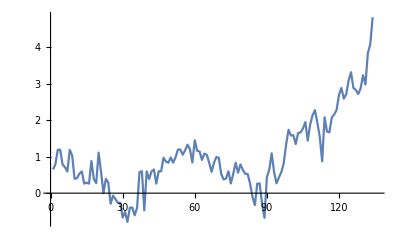
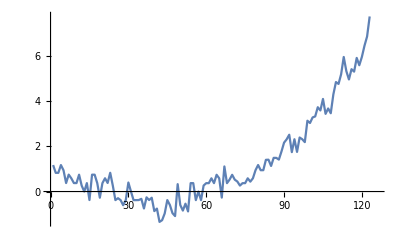
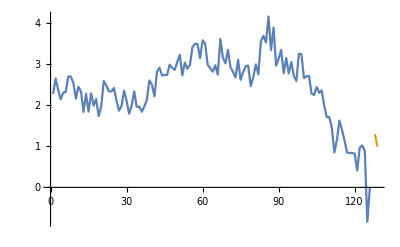
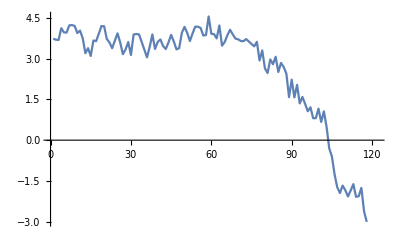
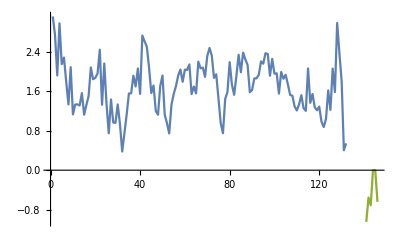
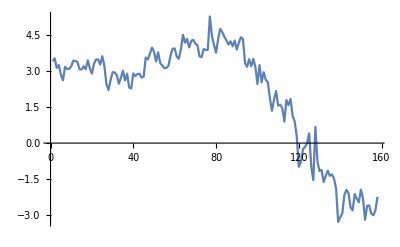
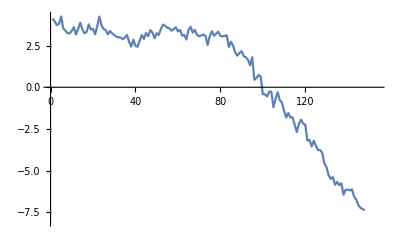
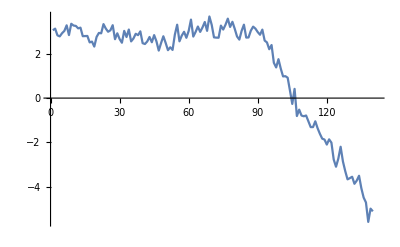
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[signChangingTraces[[#]]]&/@Range[20]
```

#### Initially degenerate vertices

Observation: many of the long lived degenerate vertices exist from the start. In this case distinguishing between T1 and rebound doesn’t really make sense. 

Criterion for initial degenerate vertices: maximum inner edge length before it first drops below 1 is < 2.

```mathematica
degLengthThr=1.0;
```

```mathematica
Function[{lengthTS},With[{
(* First time the vertex is degenerate *)
idx1=First@FirstPosition[lengthTS[[All,2]],_?(Abs[#]<degLengthThr&),{-1},{1},Heads->False]
},
Max[Take[lengthTS[[All,2]],{1,idx1}]]
]]@signChangingTraces[[2,1]]
```

1.17267

```mathematica
initiallyDegenerateTraces=Select[
signChangingTraces,
#[[1,1,1]]==1&&Function[{lengthTS},With[{
(* First time the vertex is degenerate *)
idx1=First@FirstPosition[lengthTS[[All,2]],_?(Abs[#]<degLengthThr&),{-1},{1},Heads->False]
},
Max[Take[lengthTS[[All,2]],{1,idx1}]]<2.0
]]@#[[1]]&
];
```

```mathematica
initiallyDegenerateTraces//Length
```

374

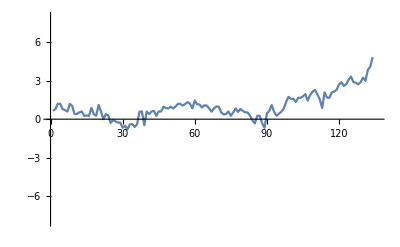
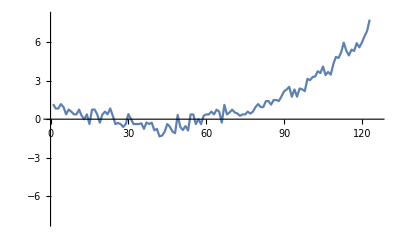
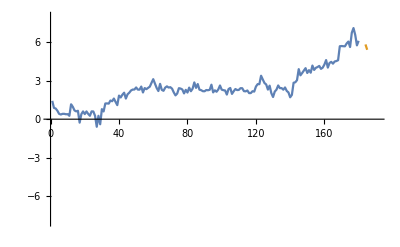
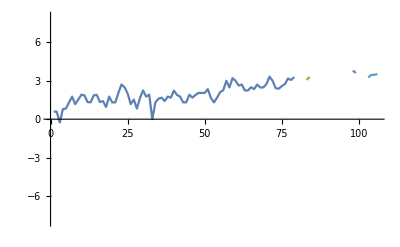
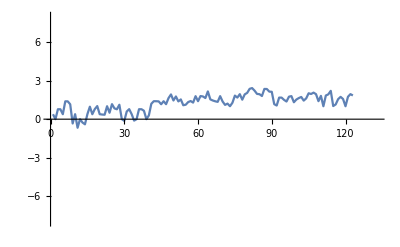
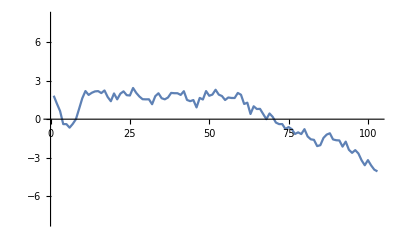
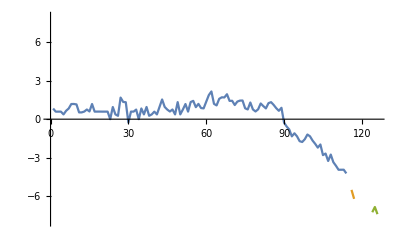
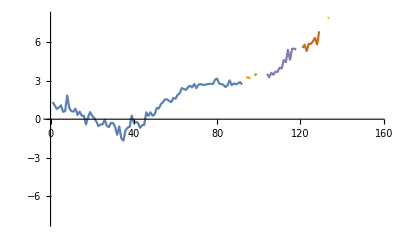

```mathematica
Tooltip[ListLinePlot[initiallyDegenerateTraces[[#]],PlotRange->{-8,8}],#]&/@Range[10]
```

```mathematica
With[{cells=Keys[initiallyDegenerateTraces][[6]]},
Manipulate[Graphics[{FaceForm[LightGray],EdgeForm[Black],renderCell2D[#,t]&/@cells}],{t,1,198,1}]
]
```

#### Rosettes (both formation and resolution!)

For each interval, test whether the length at the first frame or last frame of the interval is shorter than 1 µm.

```mathematica
degLengthThr=1.0;
rosetteTraces=Select[
quartetInnerEdgeLength,
Min[
(* If the first interval starts at time 1, ignore it, since it is an initially degenerate quartet *)
If[#[[1,1,1]]==1,
Abs[#[[2;;-1,1]][[All,2]]],
Abs[#[[All,1]][[All,2]]]
],
Abs[#[[All,-1]][[All,2]]]
]<degLengthThr&
];
```

```mathematica
rosetteTraces//Length
```

1034

This number fits quite well to the total number of rosettes (about 500). Basically, each rosette needs to edge collapses to form and two edge creations to resolve, giving 4 x 500 = 2000 events. (5-rosette annihilates two quartets and creates two new ones). Of course, not all rosettes resolve, which is compensated by 6-and 7-rosettes which involve more collapses/resolutions.

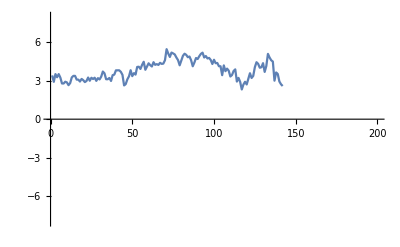
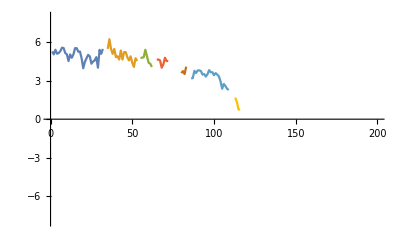
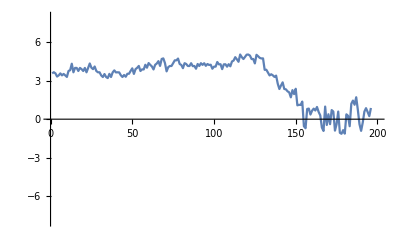
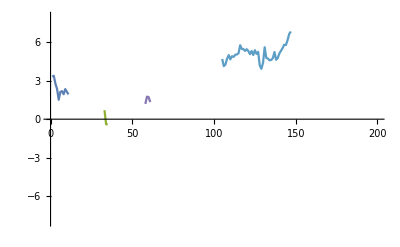
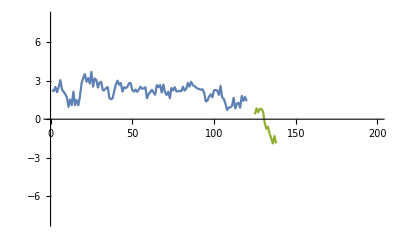
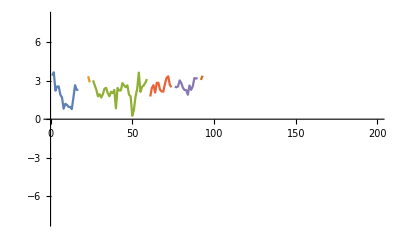
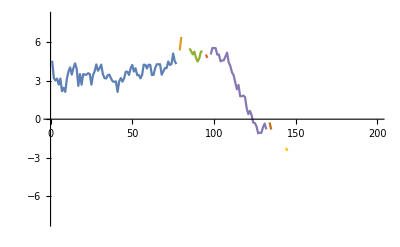
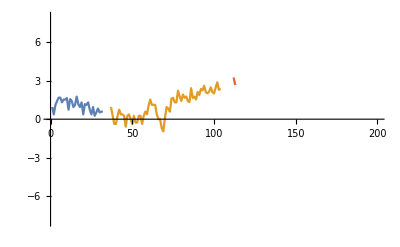

```mathematica
Tooltip[ListLinePlot[rosetteTraces[[#]],PlotRange->{{0,200},{-8,8}}],#]&/@Range[500,520]
```

```mathematica
With[{cells=Keys[rosetteTraces][[19]]},
Manipulate[Graphics[{FaceForm[LightGray],EdgeForm[Black],renderCell2D[#,t]&/@cells}],{t,1,198,1}]
]
```

Rosettes that form from initially degenerate vertices

```mathematica
Intersection[Keys[rosetteTraces],Keys[initiallyDegenerateTraces]]//Length
```

82

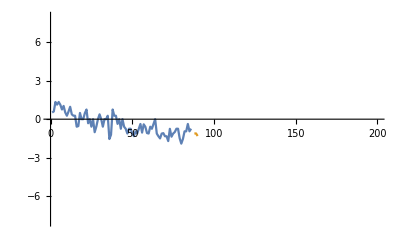
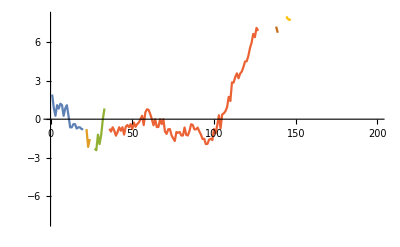
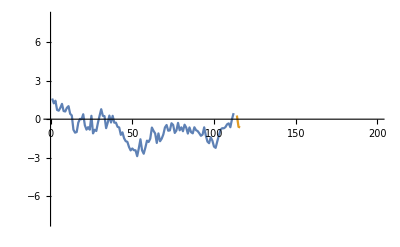
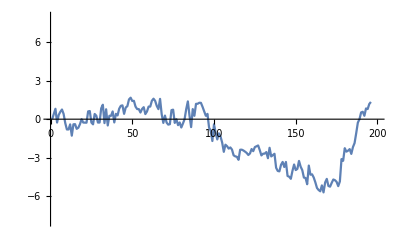
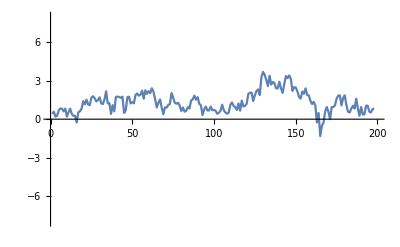
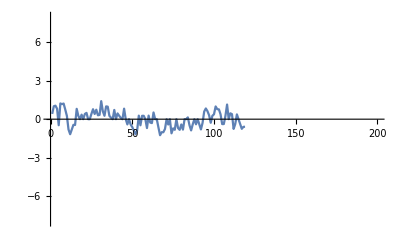
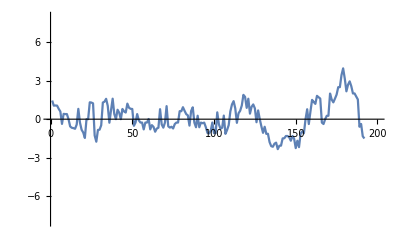
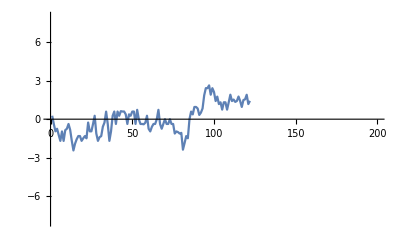
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[rosetteTraces[#],PlotRange->{{0,200},{-8,8}}]&/@Take[Intersection[Keys[rosetteTraces],Keys[initiallyDegenerateTraces]],20]
```

#### T1 traces

```mathematica
T1Traces=KeyTake[
signChangingTraces,
Complement[
Keys[Select[
signChangingTraces,
(* Make sure that the sign change (T1) happens while the quartet is intact *)
#[[-1,-1,2]]<0.&&Count[#,_?(#[[1,2]]>0.&&#[[-1,2]]<0.&)]>0&]
],
(* Exclude rosettes and initially degenrate quartets *)
Keys[rosetteTraces],Keys[initiallyDegenerateTraces]]
];
```

```mathematica
Length[T1Traces]
```

1930

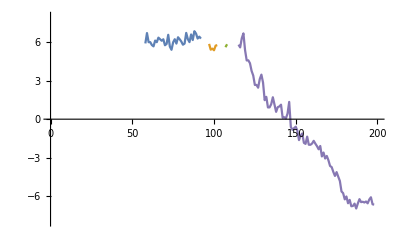
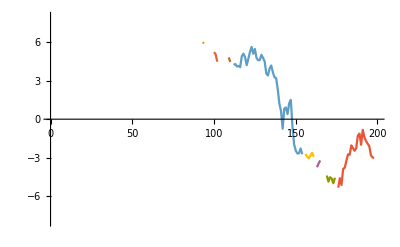
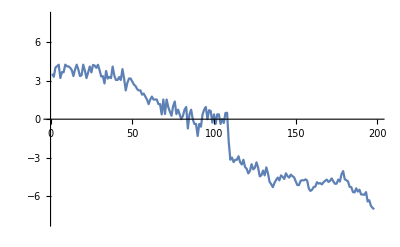
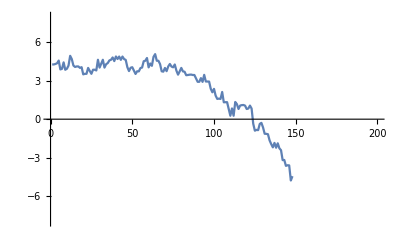
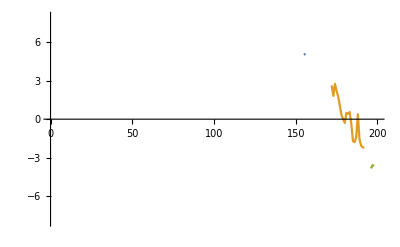
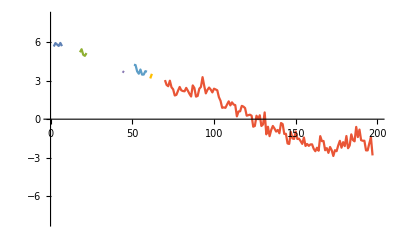
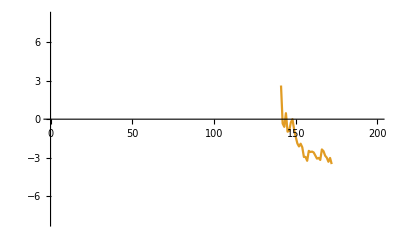
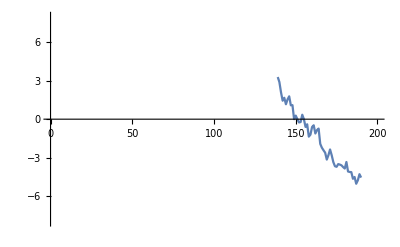

```mathematica
Tooltip[ListLinePlot[T1Traces[[#]],PlotRange->{{0,200},{-8,8}}],#]&/@Range[20]
```

```mathematica
T1Intervals=SelectFirst[#,#[[1,2]]>0.&&#[[-1,2]]<0.&][[{1,-1},1]]&/@T1Traces;
```

Write to file

```mathematica
Export[NotebookDirectory[]<>"T1-quartet-intervals.csv",KeyValueMap[Join[##]&,T1Intervals]]
```

/Users/Fridtjof.Brauns/KITP/GBE/Experiment Data/Data Tomer/T1-quartet-intervals.csv

## Tension–isogonal decompostion

Load existence time intervals for cell quartets that undergo T1s

```mathematica
T1Intervals=Association[#[[1;;4]]->#[[5;;6]]&/@Import[NotebookDirectory[]<>"../T1-quartet-intervals.csv"]];
```

#### Analysis setup for quartet tension–isogonal decomposition

```mathematica
smoothVertexPositions[quartetCoordsTS_,n_]:=Module[{
centroids,pre,post,outer
},
centroids=GaussianFilter[quartetCoordsTS[[All,1]],{{n,0,0}}];

(* Separate the time traces of the inner vertices into before and after T1. Fill in with (0,0) *)
pre=If[#[[3]],{{0.,0.},{0.,0.}},#[[2,{1,2}]]]&/@quartetCoordsTS;
post=If[!#[[3]],{{0.,0.},{0.,0.}},#[[2,{1,2}]]]&/@quartetCoordsTS;
outer=#[[2,3;;-1]]&/@quartetCoordsTS;

pre=GaussianFilter[pre,{{n,0,0}}];
post=GaussianFilter[post,{{n,0,0}}];
outer=GaussianFilter[outer,{{n,0,0}}];

MapIndexed[{centroids[[#2[[1]]]],Join[If[#1[[3]],post[[#2[[1]]]],pre[[#2[[1]]]]],outer[[#2[[1]]]]],#1[[3]]}&,quartetCoordsTS]
]
```

```mathematica
quartetInnerAngles[quartetVertexCoords_,flip_]:=Module[{ri=quartetVertexCoords,e0,e1,e2,e3,e4,e5},
e0=ri[[2]]-ri[[1]];
e1=ri[[3]]-ri[[1]];
e3=ri[[5]]-ri[[2]];
If[!flip,
e2=ri[[4]]-ri[[1]];
e4=ri[[6]]-ri[[2]];,
(* Inner edge flipped *)
e2=ri[[4]]-ri[[2]];
e4=ri[[6]]-ri[[1]];
];
With[{n0={-e0[[2]],e0[[1]]}/√(e0.e0+$MachineEpsilon)},
{
If[e0.e1<0,π-#,#]&@ArcSin[n0.e1/√(e1.e1+$MachineEpsilon)],
If[e0.e2<0,π-#,#]&@ArcSin[-n0.e2/√(e2.e2+$MachineEpsilon)],
If[e0.e3>0,π-#,#]&@ArcSin[-n0.e3/√(e3.e3+$MachineEpsilon)],
If[e0.e4>0,π-#,#]&@ArcSin[n0.e4/√(e4.e4+$MachineEpsilon)]
}
]];
quartetInnerAngles[{e0_,e1_,e2_,e3_,e4_}]:=
With[{n0={-e0[[2]],e0[[1]]}/√(e0.e0+$MachineEpsilon)},
{
If[e0.e1<0,π-#,#]&@ArcSin[n0.e1/√(e1.e1+$MachineEpsilon)],
If[e0.e2<0,π-#,#]&@ArcSin[-n0.e2/√(e2.e2+$MachineEpsilon)],
If[e0.e3>0,π-#,#]&@ArcSin[-n0.e3/√(e3.e3+$MachineEpsilon)],
If[e0.e4>0,π-#,#]&@ArcSin[n0.e4/√(e4.e4+$MachineEpsilon)]
}
]
```

Find the tension kite (pair of tension triangles)

```mathematica
triArea::neg="Negative triangle area. Check edge ordering/orientation.";
triArea[e1_,e2_]:=If[#<0,Message[triArea::neg];Abs[#],#]&@(e1[[1]]e2[[2]]-e1[[2]]e2[[1]])/2
```

```mathematica
getKite[vertexCoords:{{_?numericQ,_?numericQ}..},flip:(True|False)]:=Module[{tensions,eVecs,tVecs,A},
If[flip,
eVecs={#[[2]]-#[[1]],#[[3]]-#[[1]],#[[4]]-#[[2]],#[[5]]-#[[2]],#[[6]]-#[[1]]}&@vertexCoords;
tensions=quartetEdgeTensions[quartetInnerAngles[eVecs[[{1,2,5,4,3}]]]];
tVecs=MapThread[#1{{0,-1},{1,0}}.Normalize[#2]&,{tensions[[{1,2,5,4,3}]],eVecs}];
,
eVecs={#[[2]]-#[[1]],#[[3]]-#[[1]],#[[4]]-#[[1]],#[[5]]-#[[2]],#[[6]]-#[[2]]}&@vertexCoords;
tensions=quartetEdgeTensions[quartetInnerAngles[eVecs]];
tVecs=MapThread[#1{{0,-1},{1,0}}.Normalize[#2]&,{tensions,eVecs}];
];
If[Or@@Thread[tensions<0],Return[{eVecs,Missing["NegativeTensions"],flip}]];
(*A=triArea[tVecs[[5]],tVecs[[5]]]+triArea[tVecs[[4]],tVecs[[3]]];*)
If[flip,
A=triArea[tVecs[[1]],tVecs[[2]]]+triArea[tVecs[[5]],tVecs[[1]]],
A=triArea[tVecs[[2]],tVecs[[1]]]+triArea[tVecs[[5]],tVecs[[1]]]
];
tVecs=tVecs/√(A/2);(* Normalize such that the mean triangle area is 1 *)
{eVecs,tVecs,flip}
]
```

Force inference is underdetermined for degenerate (four-fold) vertices. Continuity suggests that we look for the solution that is closest to the tensions in the most recent timepoint, where the vertex in the quartet was not degenerate.

```mathematica
findDegenerateVertexTensions[eVecs_,referenceTensions:{_?numericQ..},
"ConstrainArea"->True
]:=Block[{T,t},
T=Array[t,4];
T/.Last[FindMinimum[{
Total[(T-referenceTensions)^2],
T.eVecs==0,
t[1]t[4](eVecs[[1,1]]eVecs[[4,2]]-eVecs[[1,2]]eVecs[[4,1]])+
t[3]t[2](eVecs[[3,1]]eVecs[[2,2]]-eVecs[[3,2]]eVecs[[2,1]])==2.
},
Transpose[{T,referenceTensions}]
]]
]
```

```mathematica
findDegenerateVertexTensions[eVecs_,referenceTensions:{_?numericQ..}
]:=Block[{T,t},
T=Array[t,4];
T/.Last[FindMinimum[{
Total[(T-referenceTensions)^2],
T.eVecs==0
},
Transpose[{T,referenceTensions}]
]]
]
```

```mathematica
correctDegenerateKites[kiteTS_,thrsh_,n_]:=Module[{
l0TS,
tMax=Length[kiteTS],
outerTensionsTS,
eVecs,referenceTensions,
outerTensions,tVecs
},
l0TS=Norm/@kiteTS[[All,1,1]];
outerTensionsTS=If[MissingQ[#],#,(Norm/@Rest[#[[2]]])]&/@kiteTS;
Table[
If[l0TS[[t]]>thrsh&&!MissingQ[kiteTS[[t,2]]],
kiteTS[[t]],
(* Else: below threshold / missing kite data *)
referenceTensions=Mean[DeleteMissing@Pick[
outerTensionsTS[[Max[1,t-n];;Min[t+n,tMax]]],
Thread[l0TS[[Max[1,t-n];;Min[t+n,tMax]]]>thrsh]
]];
If[referenceTensions===Mean[{}],
Missing["ReferenceTensions"],
eVecs=({{0,-1},{1,0}}.Normalize[#])&/@Rest[kiteTS[[t,1]]];
outerTensions=findDegenerateVertexTensions[eVecs,referenceTensions,"ConstrainArea"->True];
If[kiteTS[[t,3]](* flip *),
tVecs=Prepend[#,-#[[1]]-#[[4]]]&@MapThread[Times,{outerTensions,eVecs}];
(* Else *),
tVecs=Prepend[#,-#[[1]]-#[[2]]]&@MapThread[Times,{outerTensions,eVecs}];
];
{kiteTS[[t,1]],tVecs,kiteTS[[t,3]]}
]
],
{t,tMax}
]
]
```

```mathematica
getKiteVertices[tVecs_,flip_]:=If[flip,
{tVecs[[1]]/2,-tVecs[[1]]/2+tVecs[[4]],-tVecs[[1]]/2,tVecs[[1]]/2+tVecs[[2]]},
{-tVecs[[1]]/2-tVecs[[2]],tVecs[[1]]/2,tVecs[[1]]/2-tVecs[[4]],-tVecs[[1]]/2}
];
```

```mathematica
quartetKiteShapeTensors[centroids_,kite_,scaleFactor_]:=Module[{
tv=getKiteVertices@@kite[[{2,3}]],
c=centroids,
e1,e2
},
e1=Normalize[(c[[2]]-c[[4]])+{{0,1},{-1,0}}.(c[[1]]-c[[3]])];
e2={{0,-1},{1,0}}.e1;
{
Total[MapThread[#⊗#&@{e1.(#2-#1),e2.(#2-#1)}&,{c,RotateLeft[c]}]],
Total[MapThread[scaleFactor^2#⊗#&@{e1.(#2-#1),e2.(#2-#1)}&,{tv,RotateLeft[tv]}]],
fitLinearTransformation2D[scaleFactor{e1,e2}.#&/@tv,{e1,e2}.#&/@centroids,"Symmetric"]
}
]
```

```mathematica
getQuartetCoords[cells_,t_]:=Module[{
centroids,
v1,v2,v3,v4,v5,v6,
basis,origin,ri,flip,
test
},
centroids=cellCentroidsTS[[t]]/@cells;
basis=findLocalBasis[centroids];
(*origin=Mean[centroids];*)

flip=!MemberQ[cellNeighborsTS[[t]][cells[[2]]],cells[[4]]];

test=If[#==={},Return[Missing["FaultyQartet",{cells,t}]],First[#]]&;

If[!flip,
v1=test@sharedVertices[cells[[{1,2,4}]],t];
v2=test@sharedVertices[cells[[{2,3,4}]],t];,
(* Else *)
v1=test@sharedVertices[cells[[{1,3,4}]],t];
v2=test@sharedVertices[cells[[{1,2,3}]],t];
];

If[v1==v2,Return[Missing["DegenerateVertex",{cells,t}]]];

v3=test@DeleteCases[sharedVertices[cells[[{1,4}]],t],v1|v2];
v4=test@DeleteCases[sharedVertices[cells[[{1,2}]],t],v1|v2];
v5=test@DeleteCases[sharedVertices[cells[[{2,3}]],t],v1|v2];
v6=test@DeleteCases[sharedVertices[cells[[{3,4}]],t],v1|v2];

ri=vertexCoordsTS[[t,{v1,v2,v3,v4,v5,v6}]];

origin=Mean[ri[[{1,2}]]];

{
{(#-origin).basis[[1]],(#-origin).basis[[2]]}&/@centroids,
{(#-origin).basis[[1]],(#-origin).basis[[2]]}&/@ri,
flip
}
]
```

```mathematica
quartetCoordsTS[quartetCells_,{ts_,te_}]:=Module[{
cells,basis,centroids,coords,prevCoords
},
(* If needed relabel cells such that 2 and 4 initially share the inner edge *)
Which[
MemberQ[cellNeighborsTS[[ts]][quartetCells[[1]]],quartetCells[[3]]],cells=RotateLeft[quartetCells],
MemberQ[cellNeighborsTS[[ts]][quartetCells[[2]]],quartetCells[[4]]],cells=quartetCells,
True,Return[{}](* Initial quartet is degenerate *)
];

(* Fix the "chirality" of the vertex labeling *)
centroids=cellCentroidsTS[[ts]]/@cells;
basis=findLocalBasis[cellCentroidsTS[[ts]]/@cells];
If[Cross[centroids[[2]]-centroids[[1]],centroids[[3]]-centroids[[1]]].basis[[3]]<0,
cells=cells[[{1,4,3,2}]]
];

prevCoords=getQuartetCoords[cells,ts];

First@Last@Reap[Do[
coords=getQuartetCoords[cells,t];
If[MissingQ[coords],coords=prevCoords];
Sow[coords];
prevCoords=coords;,
{t,ts,te}
]]
]
```

```mathematica
trackQuartetKiteShapeTensors[quartet_,{ts_,te_},scaleFactor_]:=Module[{
coordsTS,kiteTS,kiteCorrectedTS
},
coordsTS=smoothVertexPositions[quartetCoordsTS[quartet,{ts,te}],5];
kiteTS=getKite@@#[[{2,3}]]&/@coordsTS;
kiteCorrectedTS=correctDegenerateKites[kiteTS,0.5,8];
Table[{
ts+i-1,
If[kiteTS[[i,3]],-1,1]Norm[kiteTS[[i,1,1]]](*innerEdgeLength[quartet,ts+i-1]*),
If[MissingQ[kiteCorrectedTS[[i]]],
Missing["TensionKite",{quartet,ts+i-1}],
quartetKiteShapeTensors[coordsTS[[i,1]],kiteCorrectedTS[[i]],scaleFactor]
],
Min[Norm/@Rest[kiteTS[[i,1]]]](* Minimum length of outer edges for filtering later *)
},
{i,Length[coordsTS]}
]
]
```

#### Rendering the cell edges and corresponding tension kite

```mathematica
Options[renderTensionKite]={Offset->{0,0}};
renderTensionKite[{e_,tVecs_,flip_},scaleFactor_,OptionsPattern[]]:=With[{
r0=OptionValue[Offset],t=scaleFactor tVecs
},
{
AbsolutePointSize[8],
AbsoluteThickness[3],Black,
Line[{r0-e[[1]]/2+e[[2]],r0-e[[1]]/2,r0+e[[1]]/2,r0+e[[1]]/2+e[[4]]}],
If[flip,
{
Line[{r0+e[[1]]/2,r0+e[[1]]/2+e[[3]]}],
Line[{r0-e[[1]]/2,r0-e[[1]]/2+e[[5]]}],
(* Tension triangle edges *)
RGBColor[0.8,0.2,0],Line[{r0-t[[1]]/2,r0+t[[1]]/2}],
Line[{r0+t[[1]]/2,r0+t[[1]]/2+t[[2]]}],
Line[{r0+t[[1]]/2,r0+t[[1]]/2-t[[3]]}],
Line[{r0-t[[1]]/2,r0-t[[1]]/2+t[[4]]}],
Line[{r0-t[[1]]/2,r0-t[[1]]/2-t[[5]]}],
(* Tension circumcircle *)
Gray,Dashed,AbsoluteThickness[1.5],
Circumsphere[{r0+t[[1]]/2,r0-t[[1]]/2+t[[4]],r0-t[[1]]/2}],
Circumsphere[{r0+t[[1]]/2,r0+t[[1]]/2+t[[2]],r0-t[[1]]/2}]
},
{
Line[{r0-e[[1]]/2,r0-e[[1]]/2+e[[3]]}],
Line[{r0+e[[1]]/2,r0+e[[1]]/2+e[[5]]}],
(* Tension triangle edges *)
RGBColor[0.8,0.2,0],Line[{r0-t[[1]]/2,r0+t[[1]]/2}],
Line[{r0-t[[1]]/2,r0-t[[1]]/2-t[[2]]}],
Line[{r0+t[[1]]/2,r0+t[[1]]/2+t[[3]]}],
Line[{r0+t[[1]]/2,r0+t[[1]]/2-t[[4]]}],
Line[{r0-t[[1]]/2,r0-t[[1]]/2+t[[5]]}],
(* Tension circumcircle *)
Gray,Dashed,AbsoluteThickness[1.5],
Circumsphere[{r0+t[[1]]/2,r0-t[[1]]/2-t[[2]],r0-t[[1]]/2}],
Circumsphere[{r0+t[[1]]/2,r0+t[[1]]/2-t[[4]],r0-t[[1]]/2}]
}
]
}
]
```

```mathematica
testQuartet={{13803,13854,13919,13868},{1,142}};
```

```mathematica
testCoordsTS=smoothVertexPositions[quartetCoordsTS@@testQuartet,5];
```

```mathematica
testKiteTS=getKite@@#[[{2,3}]]&/@testCoordsTS;
```

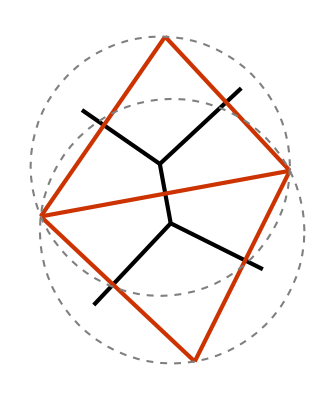

```mathematica
Graphics[renderTensionKite[#,6]&@testKiteTS[[1]]]
```

```mathematica
Manipulate[
Graphics[renderTensionKite[##,6]&@testKiteTS[[t]]],
{t,1,Length[testKiteTS],1}
]
```

Part::partd: Part specification testKiteTS⟦36⟧ is longer than depth of object.

#### Run analysis for T1 quartets in germ band (Fig. 4, 4S1)

The scale factor translates from triangle-edge lengths in tension space to centroidal distances in real space (see Appendix 3 in the manuscript). The factor 2/3^(1/4) is the triangle-edge length for an equilateral triangle with unit area. It appears because we normalize tension triangle areas to unity to fix the unknown tension scale. The factor 4.1 is found from the average spacing of neighboring cell centroids at early times, where the tensions are nearly isotropic, i.e. tension triangles are close to equilateral.

```mathematica
$scaleFactor=4.1(2/3^(1/4));
```

```mathematica
$abortExceptions=Prepend[$abortExceptions,FindMinimum::infeas];
abortOnMessageOn[]
```

```mathematica
excludeQartets={{6420,6453,6546,6503},{13522,13572,13564,13611}};
```

```mathematica
shapeTSs=With[{
germBandEvents=KeySelect[T1Intervals,!MemberQ[excludeQartets,#]&&Length[Intersection[#,bodyCellsDorsal]]==0&]
},
KeyValueMap[trackQuartetKiteShapeTensors[#1,#2,$scaleFactor]&,RandomSample[germBand,200]]
];//AbsoluteTiming
```

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

{33.6211,Null}

Align timeseries on timepoint of neighbor exchange

```mathematica
shapeTSsAligned=Map[Function[TS,
With[{t0=TS[[firstSignChangePos[TS[[All,2]]],1]]},Prepend[Rest[#],#[[1]]-t0]&/@DeleteCases[TS,{_,_,_Missing,_}]]
],
Select[shapeTSs,Length[#]>30&](* Include only traces that are longer than 30 timepoints (7.5 min) *)
];
```

Plot log ratio of AP-AP to DV-DV component of the shape tensors 
First as a function of time (Fig. 4S1)

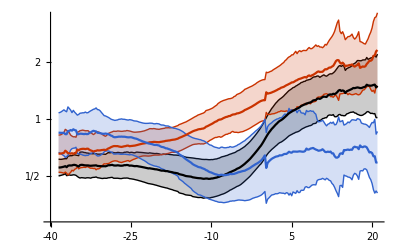

```mathematica
With[{
(* Cell centroids = physical shape change *)
dataC=binByFirst[Catenate[Transpose[{
#[[All,1]],
1/2(Log2[#[[All,3,1,1,1]]]-Log2[#[[All,3,1,2,2]]])
}]&/@(Select[#,#[[-1]]>0.5&]&/@shapeTSsAligned)]],
(* Tension vertices = tension space shape change *)
dataT=binByFirst[Catenate[Transpose[{
#[[All,1]],
1/2(Log2[#[[All,3,2,1,1]]]-Log2[#[[All,3,2,2,2]]])
}]&/@(Select[#,#[[-1]]>0.5&]&/@shapeTSsAligned)]],
(* Isogonal deformation *)
dataI=binByFirst[Catenate[Transpose[{
#[[All,1]],
(Log2[#[[All,3,3,1,1]]]-Log2[#[[All,3,3,2,2]]])
}]&/@(Select[#,#[[-1]]>0.5&&#[[3,3,1,1]]>0&&#[[3,3,2,2]]>0&]&/@shapeTSsAligned)]]
},
ListLinePlot[{
{#[[1]]/4,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[dataC,Length[#[[2]]]>10&],
{#[[1]]/4,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[dataT,Length[#[[2]]]>10&],
{#[[1]]/4,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[dataI,Length[#[[2]]]>10&]
},
PlotStyle->{Black,ColorData[112,1],ColorData[112,2]},
IntervalMarkers->"Bands",
PlotRange->{-1.8,1.8},
AxesOrigin->{-40,-1.8},
Ticks->{Range[-40,20,5],{{-1,1/2},{Log2[1./√3],""},{0,1},{Log2[√3],""},{1,2}}}
]
]
```

Plots as a function of inner-edge length, which serves as a pseudotime for the T1 process (Fig. 4)

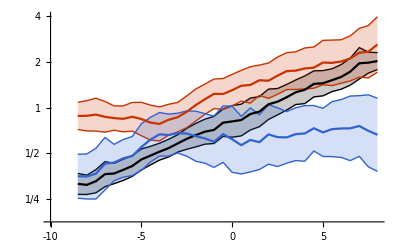

```mathematica
With[{
dataC=Catenate[Transpose[{
-#[[All,2]],
1/2(Log2[#[[All,3,1,1,1]]]-Log2[#[[All,3,1,2,2]]])
}]&/@(Select[#,#[[-1]]>0.5&]&/@shapeTSsAligned)],
dataT=Catenate[Transpose[{
-#[[All,2]],
1/2(Log2[#[[All,3,2,1,1]]]-Log2[#[[All,3,2,2,2]]])
}]&/@(Select[#,#[[-1]]>0.5&]&/@shapeTSsAligned)],
dataI=Catenate[Transpose[{
-#[[All,2]],
(Log2[#[[All,3,3,1,1]]]-Log2[#[[All,3,3,2,2]]])
}]&/@(Select[#,#[[-1]]>0.5&&#[[3,3,1,1]]>0&&#[[3,3,2,2]]>0&]&/@shapeTSsAligned)]
},
ListLinePlot[{
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[binByFirst[dataC,0.5],Length[#[[2]]]>50&],
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[binByFirst[dataT,0.5],Length[#[[2]]]>50&],
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[binByFirst[dataI,0.5],Length[#[[2]]]>50&]
},
PlotStyle->{Black,ColorData[112,1],ColorData[112,2]},
IntervalMarkers->"Bands",
PlotRange->{-2.5,2},
AxesOrigin->{-10,-2.5},
Ticks->{Join[Range[-10,10,5],{{-3.5,""},{4.5,""}}],{{-2,1/4},{-1,1/2},{0,1},{1,2},{2 ,4}}}
]
]
```

#### Amnioserosa (dorsal pole)

```mathematica
shapeTSsDorsal=With[{
dorsalEvents=KeySelect[T1Intervals,Length[Intersection[#,bodyCellsDorsal]]>0&]
},
KeyValueMap[trackQuartetKiteShapeTensors[#1,#2,$scaleFactor]&,dorsalEvents]
];//AbsoluteTiming
```

{14.7044,Null}

```mathematica
shapeTSsAligned=Function[TS,With[{t0=TS[[firstSignChangePos[TS[[All,2]]],1]]},Prepend[Rest[#],#[[1]]-t0]&/@DeleteCases[TS,{_,_,_Missing,_}]]]/@shapeTSsDorsal;
```

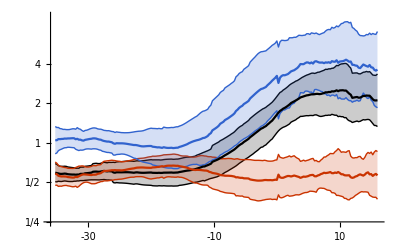

```mathematica
With[{
dataC=binByFirst[Catenate[Transpose[{
#[[All,1]],
1/2(Log2[#[[All,3,1,1,1]]]-Log2[#[[All,3,1,2,2]]])
}]&/@(Select[#,#[[-1]]>0.5&]&/@shapeTSsAligned)]],
dataT=binByFirst[Catenate[Transpose[{
#[[All,1]],
1/2(Log2[#[[All,3,2,1,1]]]-Log2[#[[All,3,2,2,2]]])
}]&/@(Select[#,#[[-1]]>0.5&]&/@shapeTSsAligned)]],
dataI=binByFirst[Catenate[Transpose[{
#[[All,1]],
(Log2[#[[All,3,3,1,1]]]-Log2[#[[All,3,3,2,2]]])
}]&/@(Select[#,#[[-1]]>0.5&&#[[3,3,1,1]]>0&&#[[3,3,2,2]]>0&]&/@shapeTSsAligned)]]
},
ListLinePlot[{
{#[[1]]/4,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[dataC,Length[#[[2]]]>10&],
{#[[1]]/4,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[dataT,Length[#[[2]]]>10&],
{#[[1]]/4,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[dataI,Length[#[[2]]]>10&]
},
PlotStyle->{Black,ColorData[112,1],ColorData[112,2]},
IntervalMarkers->"Bands",
PlotRange->{-2,3.2},
AxesOrigin->{-36,-2},
Ticks->{Range[-30,20,10],Table[{x,2^x},{x,-2,2,1}]}
]
]
```

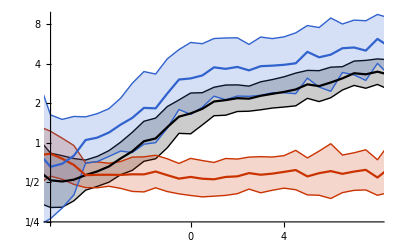

```mathematica
With[{
dataC=Catenate[Transpose[{
-#[[All,2]],
1/2(Log2[#[[All,3,1,1,1]]]-Log2[#[[All,3,1,2,2]]])
}]&/@(Select[#,#[[-1]]>0.5&]&/@shapeTSsAligned)],
dataT=Catenate[Transpose[{
-#[[All,2]],
1/2(Log2[#[[All,3,2,1,1]]]-Log2[#[[All,3,2,2,2]]])
}]&/@(Select[#,#[[-1]]>0.5&]&/@shapeTSsAligned)],
dataI=Catenate[Transpose[{
-#[[All,2]],
(Log2[#[[All,3,3,1,1]]]-Log2[#[[All,3,3,2,2]]])
}]&/@(Select[#,#[[-1]]>0.5&&#[[3,3,1,1]]>0&&#[[3,3,2,2]]>0&]&/@shapeTSsAligned)]
},
ListLinePlot[{
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[binByFirst[dataC,0.5],Length[#[[2]]]>10&],
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[binByFirst[dataT,0.5],Length[#[[2]]]>10&],
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[binByFirst[dataI,0.5],Length[#[[2]]]>10&]
},
PlotStyle->{Black,ColorData[112,1],ColorData[112,2]},
IntervalMarkers->"Bands",
PlotRange->{{-6,8},{-2,3.2}},
AxesOrigin->{-6,-2},
Ticks->{Join[Range[-10,10,5],{-3.5,4}],Table[{x,2^x},{x,-2,3,1}]}
]
]
```